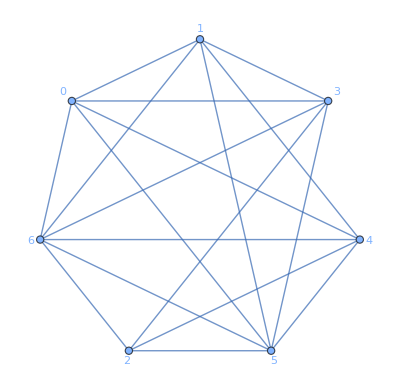

```mathematica
colourGraph=Graph[
Range[0,6],
{
4<->0,6<->3,4<->2,5<->4,0<->1,3<->1,1<->4,6<->0,5<->3,5<->2,5<->1,2<->3,6<->1,4<->6,5<->0,3<->0,6<->5,2<->6
},
VertexLabels->"Name", GraphLayout->"CircularEmbedding"
]
```

```mathematica
ChromaticPolynomial[colourGraph]
```

Function[x,408 x-1042 x^2+1019 x^3-500 x^4+132 x^5-18 x^6+x^7]

Find both the chromatic number and number of vertex colourings using a range, the first non-0 input is the chromatic number, and then read off the number of vertex colourings

```mathematica
colourings = AssociationMap[ChromaticPolynomial[colourGraph], Range[10]]
```

<|1→0,2→0,3→0,4→0,5→240,6→3600,7→25200,8→114240,9→393120,10→1118880|>